# Just-In-Time Machine Learning (JITML)

## A self-evolving architecture

Ghetea Patrick

Copyright (c) 2026 Ghetea Patrick. All rights reserved.

## Abstract

Just-In-Time Machine Learning (JITML) is a proposed way to adapt a model while it is running. Instead of relying on one fixed task network for every situation, a suite of meta-networks generates compact specialists when an unfamiliar context appears.

This notebook presents the architecture and a small red-and-blue tile experiment. The Python snippets are the supplied structural template: their formatting and placeholders are preserved, and they are displayed as non-evaluating code blocks.

## The limits of a fixed starting point

Ahead-Of-Time Machine Learning (AOTML), as used here, means preparing a network before deployment and keeping its task structure fixed during use. That starting point works while the situations it encounters remain close to what it was prepared for. A change in context can call for an update or a different specialist.

JITML explores a different runtime path: keep a useful baseline, reuse specialists for familiar contexts, and generate a new task network when the existing ones no longer fit. The aim is to handle a new context without retraining the entire system at every encounter. The meta-networks still need an initial training process and later updates.

## Core components

Task-networks (TNNs) do the immediate work. Each is a compact feed-forward neural network associated with a field of expertise: a group of contexts for which it is useful.

Meta-networks (MNNs) build those specialists. The suite separates four decisions: SNN defines the shape, ANN chooses activations, WNN supplies weights, and BNN supplies bias values. The proposed MNNs also use feed-forward designs.

Two pipelines connect them. The Task Generation Pipeline (TGP) creates a specialist at runtime. The Meta Training Pipeline (MTP) learns from accumulated context–TNN pairs so that later specialists can start from better proposals.

## Task Generation Pipeline (TGP)

An unfamiliar context enters a sequence of generators. Each stage fills in one part of the new network definition, building on the choices made before it.

#### SNN · Shape

The SNN proposes which neuron slots are active. In the proposed design, sigmoid outputs are interpreted as an on/off mask; slots that do not contain neurons are removed.

#### ANN · Activations

The ANN uses the structural description to choose the activation function for each layer.

#### WNN and BNN · Parameters

The WNN fills the network with weights, and weights close to zero can be pruned. The BNN completes the bias values, matching the gen_biasvalue() interface in the Python template. The intended result is a compact TNN before candidate selection begins.

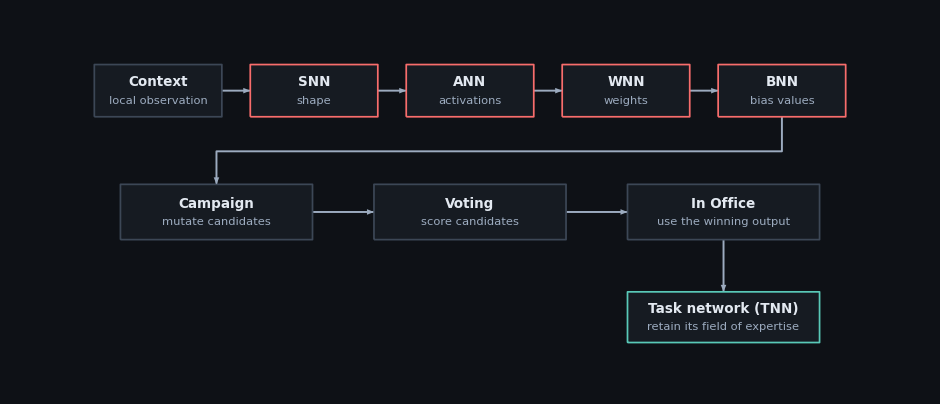

#### Campaign → Voting → In Office

Campaign creates candidates by mutating the proposed TNN parameters. Voting scores those candidates using a fixed set of criteria. In Office uses the winning output and retains the TNN that produced it, together with the context that establishes its field of expertise.

The initial voting idea favors clear, predominant outputs with lower entropy. In the toy experiment, task feedback must also show whether the chosen behavior works: a confident output can still select the wrong move. Deterministic scoring makes the decision repeatable for a fixed candidate set; it does not make candidate generation deterministic.

The arrows show the intended staged data flow. The supplied TGP snippet names the generators and selection steps; context passing, compatibility checks and candidate scoring remain implementation details.

## TNN lifecycle

For each context, the system first looks for a TNN with a matching field of expertise. A match reuses the existing specialist. Otherwise, the TGP creates a new one.

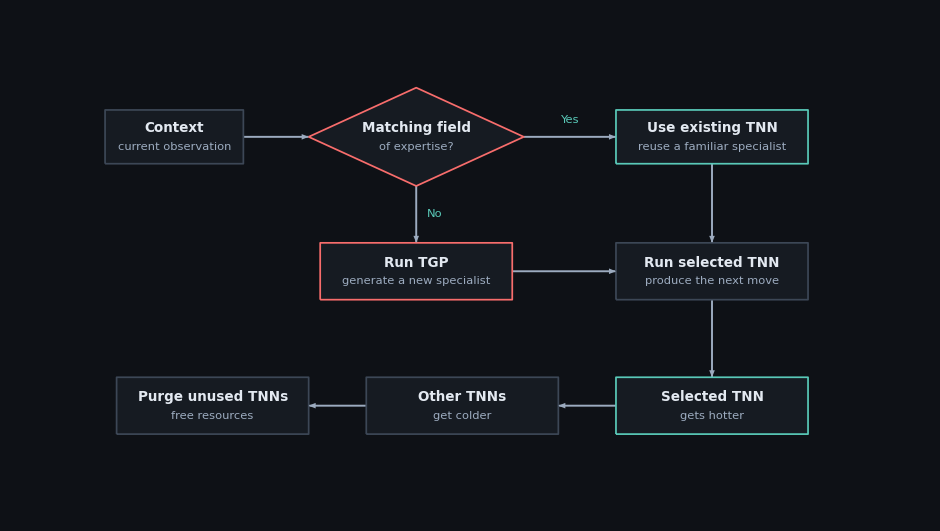

A selected TNN becomes hotter, while unused TNNs become colder. Networks that remain unused are purged to release resources. The lifespan fields in Net and the matching and lifecycle hooks in Step provide places to implement this policy; the thresholds and matching rule are deliberately left open.

## Meta Training Pipeline (MTP)

The MTP bootstraps the generators from known contexts and their associated TNNs. The context bank is the conceptual record of those pairs; currinput and pastinput provide places to retain observations alongside each network.

Each MNN learns its own part of the network definition: shapes for SNN, activation choices for ANN, weights for WNN, and biases for BNN. A candidate suite is checked with the selection criteria and benchmarked against the current suite on known context–TNN pairs before it is accepted.

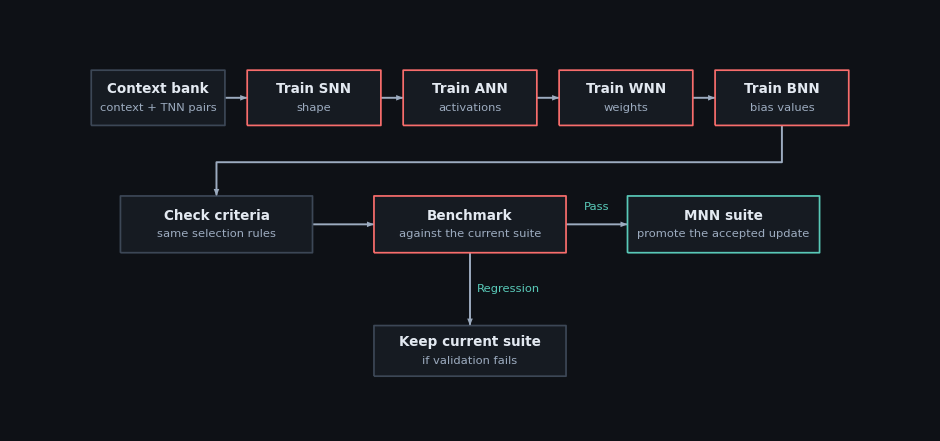

If the update fails those checks, the current suite stays in use. This feedback loop is the proposed route to better initial TNNs over time; the notebook does not claim measured improvement. The short MTP function below marks the training entry point, while validation and promotion remain to be implemented.

## A toy problem: red and blue tiles

The proposed test uses a grid with two tile types. Blue and red tiles have different mappings from the agent’s four move commands to physical directions. The goal is to see whether the system can keep a useful specialist through small changes, then generate another one when the changed surroundings require different behavior.

The supplied environment already defines the board, the player position, a local view and basic movement. With the default settings, the board is 16 × 16, the agent starts at row 8 and column 0, and radius 1 gives a local window of up to 3 × 3 cells. Blue becomes less likely down the board as red becomes more likely. A run finishes when the agent reaches the last row.

The tile-dependent direction mappings are part of the proposed experiment. Env.move() currently applies the four directions directly, so those mappings and the learning behavior are not yet implemented in this skeleton. The code is kept exactly as supplied.

A useful trial begins with familiar local contexts, introduces a few changed tiles, then exposes the agent to enough of the other tile system to make the old specialist a poor match. The expected pattern to test is reuse, generation, and then reuse of the new specialist. A small visual change alone should not force a new TNN if the current behavior still works.

To assess that pattern, a later implementation can record when generation happens, which TNN is selected, how long specialists remain active, and whether the agent reaches the goal. These are proposed observations for the experiment, rather than results from the current template.

## Python structure

The seven modules below appear in the supplied order. Each code block preserves the original text, including indentation, alignment, naming and ellipses. They document the architecture and are not evaluated by this notebook.

### defval.py · Default network definitions

This module reserves the layer sizes, activation functions, weights and biases for the TNN and each MNN. The empty lists leave the baseline configuration open while keeping the same four-part description across every network type.

#defval.py

from netdef import Cube, Grid

TNN_LAYERSIZE: list[int]   = []
TNN_ACTIVFUNC: list        = []
TNN_WEIGVALUE: Cube[float] = []
TNN_BIASVALUE: Grid[float] = []

SNN_LAYERSIZE: list[int]   = []
SNN_ACTIVFUNC: list        = []
SNN_WEIGVALUE: Cube[float] = []
SNN_BIASVALUE: Grid[float] = []

ANN_LAYERSIZE: list[int]   = []
ANN_ACTIVFUNC: list        = []
ANN_WEIGVALUE: Cube[float] = []
ANN_BIASVALUE: Grid[float] = []

WNN_LAYERSIZE: list[int]   = []
WNN_ACTIVFUNC: list        = []
WNN_WEIGVALUE: Cube[float] = []
WNN_BIASVALUE: Grid[float] = []

BNN_LAYERSIZE: list[int]   = []
BNN_ACTIVFUNC: list        = []
BNN_WEIGVALUE: Cube[float] = []
BNN_BIASVALUE: Grid[float] = []

### envdef.py · The environment and local context

Specs holds the grid settings and display values. numgrid() builds the red-and-blue distribution, while strgrid() renders it. Env owns the current position, clamps movement at the board edges, and exposes both a full view and the nearby context through near().

The random generator is created once with Random(42). The near() window is clipped at the board boundaries, so the template leaves the later network implementation to decide how observations of different sizes will be represented.

# envdef.py

from dataclasses import dataclass
from enum import auto, Enum
from random import Random

from netdef import Grid

ansiblu = "\033[34m"
ansired = "\033[31m"
ansirst = "\033[0m"
ansicls = "\033[2J\033[H"

randgen = Random(42)


class Move(Enum):
    Up = auto()
    Dn = auto()
    Lf = auto()
    Rg = auto()


@dataclass
class Specs:
    bluini: int = 16
    bludif: int = 1
    bluval: int = 0
    blustr: str = ansiblu + "B" + ansirst

    redini: int = 0
    reddif: int = 1
    redval: int = 1
    redstr: str = ansired + "R" + ansirst

    youval: int = 2
    youstr: str = "Y"

    rownum: int = 16
    rowini: int = 8

    colnum: int = 16
    colini: int = 0

    sedval: int = 42
    radius: int = 1


def numgrid(specs: Specs) -> Grid[int]:
    probblu = specs.bluini
    probred = specs.redini
    newgrid = []
    tilpick = 0

    for _ in range(specs.rownum):
        probblu -= specs.bludif if probblu > 0 else 0
        probred += specs.reddif if probred >= 0 else 0

        temprow = []
        for _ in range(specs.colnum):
            tilpick = randgen.choices([specs.bluval, specs.redval], [probblu, probred])[0]
            temprow.append(tilpick)
        newgrid.append(temprow)

    return newgrid


def strgrid(grid: Grid[int], specs: Specs) -> str:
    newgrid = []

    blu_youval = specs.youval + specs.bluval
    red_youval = specs.youval + specs.redval

    for row in grid:
        temprow = ""
        for cel in row:
            if cel == specs.bluval:
                temprow += specs.blustr
            if cel == specs.redval:
                temprow += specs.redstr
            if cel == blu_youval:
                temprow += specs.youstr
            if cel == red_youval:
                temprow += specs.youstr
        newgrid.append(temprow)

    return "\n".join(newgrid)


class Env:
    def __init__(self, specs: Specs = Specs()) -> None:
        self.mygrid = numgrid(specs)
        self.myspec = specs
        self.rowcur = specs.rowini
        self.colcur = specs.colini

    def __str__(self) -> str:
        return strgrid(self.view(), self.myspec)

    def done(self) -> bool:
        return bool(self.rowcur == self.myspec.rownum - 1)

    def move(self, move: Move) -> None:
        if move == Move.Up:
            self.rowcur -= 1
        if move == Move.Dn:
            self.rowcur += 1
        if move == Move.Lf:
            self.colcur -= 1
        if move == Move.Rg:
            self.colcur += 1

        self.rowcur = max(0, min(self.rowcur, self.myspec.rownum - 1))
        self.colcur = max(0, min(self.colcur, self.myspec.colnum - 1))

    def view(self) -> Grid[int]:
        grid = [row[:] for row in self.mygrid]
        grid[self.rowcur][self.colcur] += self.myspec.youval
        return grid

    def near(self) -> Grid[int]:
        grid = self.view()

        rowmax = min(self.myspec.rownum, self.rowcur + self.myspec.radius + 1)
        rowmin = max(0, self.rowcur - self.myspec.radius)

        colmax = min(self.myspec.colnum, self.colcur + self.myspec.radius + 1)
        colmin = max(0, self.colcur - self.myspec.radius)

        return [row[colmin:colmax] for row in grid[rowmin:rowmax]]

### jitdef.py · Shared state and the runtime loop

Ctx collects the environment, timing fields, TNN queues and the four MNNs. The jitml() loop makes the intended order visible: check completion, render, handle lifecycle work, request generation when needed, make a move, and check whether meta-training is due.

The queues and Step methods mark the boundaries between those responsibilities. Their detailed policies remain open, so the notebook can explain the system without choosing a full implementation.

# jitdef.py

from dataclasses import dataclass

from envdef import Env
from netdef import Ann, Bnn, Snn, Wnn, Que, Tnn
from stepdef import Step


@dataclass
class Ctx:
    runme: bool = True

    every: int = 32
    ticks: int = 64
    clock: int = 0

    myenv: Env = Env()

    myque: Que = []
    okque: Que = []
    dfque: Que = [Tnn()]

    mysnn: Snn = Snn()
    myann: Ann = Ann()
    mywnn: Wnn = Wnn()
    mybnn: Bnn = Bnn()


def jitml(ctx: Ctx) -> None:
    while ctx.runme:
        Step.doneplay(ctx)
        Step.uirender(ctx)
        Step.keepbusy(ctx)
        Step.killdead(ctx)
        Step.givelife(ctx)
        Step.needstgp(ctx)
        Step.makemove(ctx)
        Step.needsmtp(ctx)

### mtpdef.py · The meta-training entry point

MTP() sends the current TNN queue to each generator’s trainme() method. It is the compact entry point for the learning phase described above. Extracting training pairs, fitting each MNN and deciding whether to accept an update belong inside the later training and validation implementation.

# mtpdef.py

from jitdef import Ctx


def MTP(ctx: Ctx) -> None:
    ctx.mysnn.trainme(ctx.myque)
    ctx.myann.trainme(ctx.myque)
    ctx.mywnn.trainme(ctx.myque)
    ctx.mybnn.trainme(ctx.myque)

### netdef.py · Network types and generation interfaces

Grid, Cube and Tess describe nested list shapes, while Ten names the tensor type. Net stores a common network definition, its current and past inputs, and the fields used for matching and lifecycle decisions.

Tnn adds the move-generation interface. Snn, Ann, Wnn and Bnn each expose the part of a new TNN they are responsible for producing. The forward(), trainme() and generation methods intentionally remain placeholders. Their bodies, type syntax, spacing and class layout are preserved below.

# netdef.py

from torch import Tensor

import defval
from envdef import Move

type Mnn = Snn | Ann | Wnn | Bnn
type Que = list[Tnn]

type Grid[T] = list[list[T]]
type Cube[T] = list[Grid[T]]
type Tess[T] = list[Cube[T]]

type Ten = Tensor


class Net:
    def __init__(
        self,
        layersize: list[int],
        activfunc: list,
        weigvalue: Cube[float],
        biasvalue: Grid[float],
        currinput: Grid[int],
        pastinput: Cube[int],
        lifescore: int,
        lifelimit: int,
        goodmatch: bool
    ) -> None:
        self.layersize = layersize
        self.activfunc = activfunc
        self.weigvalue = weigvalue
        self.biasvalue = biasvalue
        self.currinput = currinput
        self.pastinput = pastinput
        self.lifescore = lifescore
        self.lifelimit = lifelimit
        self.goodmatch = goodmatch

    def forward(self, ten: Ten) -> ...:
        ...

    def trainme(self, que: Que) -> ...:
        ...


class Tnn(Net):
    def __init__(
        self,
        layersize: None | list[int]   = None,
        activfunc: None | list        = None,
        weigvalue: None | Cube[float] = None,
        biasvalue: None | Grid[float] = None,
        currinput: None | Grid[int]   = None,
        pastinput: None | Cube[int]   = None,
        lifescore: None | int         = None,
        lifelimit: None | int         = None,
        goodmatch: None | bool        = None
    ) -> None:
        super().__init__(
            layersize or defval.TNN_LAYERSIZE,
            activfunc or defval.TNN_ACTIVFUNC,
            weigvalue or defval.TNN_WEIGVALUE,
            biasvalue or defval.TNN_BIASVALUE,
            currinput or [],
            pastinput or [],
            lifescore or 10,
            lifelimit or 0,
            goodmatch or False)

    def gen_takenmove(self) -> Move:
        ...


class Snn(Net):
    def __init__(
        self,
        layersize: None | list[int]   = None,
        activfunc: None | list        = None,
        weigvalue: None | Cube[float] = None,
        biasvalue: None | Grid[float] = None,
        currinput: None | Grid[int]   = None,
        pastinput: None | Cube[int]   = None,
        lifescore: None | int         = None,
        lifelimit: None | int         = None,
        goodmatch: None | bool        = None
    ) -> None:
        super().__init__(
            layersize or defval.SNN_LAYERSIZE,
            activfunc or defval.SNN_ACTIVFUNC,
            weigvalue or defval.SNN_WEIGVALUE,
            biasvalue or defval.SNN_BIASVALUE,
            currinput or [],
            pastinput or [],
            lifescore or 10,
            lifelimit or 0,
            goodmatch or False)

    def gen_layersize(self) -> list[int]:
        ...


class Ann(Net):
    def __init__(
        self,
        layersize: None | list[int]   = None,
        activfunc: None | list        = None,
        weigvalue: None | Cube[float] = None,
        biasvalue: None | Grid[float] = None,
        currinput: None | Grid[int]   = None,
        pastinput: None | Cube[int]   = None,
        lifescore: None | int         = None,
        lifelimit: None | int         = None,
        goodmatch: None | bool        = None
    ) -> None:
        super().__init__(
            layersize or defval.ANN_LAYERSIZE,
            activfunc or defval.ANN_ACTIVFUNC,
            weigvalue or defval.ANN_WEIGVALUE,
            biasvalue or defval.ANN_BIASVALUE,
            currinput or [],
            pastinput or [],
            lifescore or 10,
            lifelimit or 0,
            goodmatch or False)

    def gen_activfunc(self) -> list:
        ...

class Wnn(Net):
    def __init__(
        self,
        layersize: None | list[int]   = None,
        activfunc: None | list        = None,
        weigvalue: None | Cube[float] = None,
        biasvalue: None | Grid[float] = None,
        currinput: None | Grid[int]   = None,
        pastinput: None | Cube[int]   = None,
        lifescore: None | int         = None,
        lifelimit: None | int         = None,
        goodmatch: None | bool        = None
    ) -> None:
        super().__init__(
            layersize or defval.WNN_LAYERSIZE,
            activfunc or defval.WNN_ACTIVFUNC,
            weigvalue or defval.WNN_WEIGVALUE,
            biasvalue or defval.WNN_BIASVALUE,
            currinput or [],
            pastinput or [],
            lifescore or 10,
            lifelimit or 0,
            goodmatch or False)

    def gen_weigvalue(self) -> Cube[float]:
        ...

class Bnn(Net):
    def __init__(
        self,
        layersize: None | list[int]   = None,
        activfunc: None | list        = None,
        weigvalue: None | Cube[float] = None,
        biasvalue: None | Grid[float] = None,
        currinput: None | Grid[int]   = None,
        pastinput: None | Cube[int]   = None,
        lifescore: None | int         = None,
        lifelimit: None | int         = None,
        goodmatch: None | bool        = None
    ) -> None:
        super().__init__(
            layersize or defval.BNN_LAYERSIZE,
            activfunc or defval.BNN_ACTIVFUNC,
            weigvalue or defval.BNN_WEIGVALUE,
            biasvalue or defval.BNN_BIASVALUE,
            currinput or [],
            pastinput or [],
            lifescore or 10,
            lifelimit or 0,
            goodmatch or False)

    def gen_biasvalue(self) -> Grid[float]:
        ...

### stepdef.py · The runtime decisions

is_match() and is_alive() name the two central decisions: whether a TNN fits the context and whether it should remain available. Step separates rendering, lifecycle work, movement, task generation and meta-training into individual hooks called by the main loop.

This keeps the overall runtime sequence easy to inspect while leaving matching rules, lifetime updates and scheduling for the implementation stage.

# stepdef.py

from jitdef import Ctx
from netdef import Tnn
from mtpdef import MTP
from tgpdef import TGP


def is_match(tnn: Tnn, ctx: Ctx) -> bool:
    ...


def is_alive(tnn: Tnn) -> bool:
    ...


class Step:
    @staticmethod
    def doneplay(ctx: Ctx) -> None:
        ...

    @staticmethod
    def uirender(ctx: Ctx) -> None:
        ...

    @staticmethod
    def keepbusy(ctx: Ctx) -> None:
        ...

    @staticmethod
    def killdead(ctx: Ctx) -> None:
        ...

    @staticmethod
    def givelife(ctx: Ctx) -> None:
        ...

    @staticmethod
    def makemove(ctx: Ctx) -> None:
        ...

    @staticmethod
    def needstgp(ctx: Ctx) -> None:
        ...

    @staticmethod
    def needsmtp(ctx: Ctx) -> None:
        ...

### tgpdef.py · From proposals to a task network

TGP() reads the nearby grid, asks the four MNNs for initial definitions, creates candidate sets, selects values through Vote, and returns a Tnn. The names mirror the proposed generation and election process.

The current skeleton collects the context but does not yet pass it through the generators. It also votes on the definition fields separately. A later implementation must connect the staged inputs and keep the selected shape, activations, weights and biases compatible; the supplied snippet remains unchanged.

# tgpdef.py

from jitdef import Ctx
from netdef import Cube, Grid, Tess, Tnn


class Vote:
    @staticmethod
    def layersize_from(cands: Grid[int]) -> list[int]:
        ...

    @staticmethod
    def activfunc_from(cands: Grid) -> list:
        ...

    @staticmethod
    def weigvalue_from(cands: Tess[float]) -> Cube[float]:
        ...

    @staticmethod
    def biasvalue_from(cands: Cube[float]) -> Grid[float]:
        ...


def candidates_of[T](L: list[T]) -> Grid[T]:
    ...


def TGP(ctx: Ctx) -> Tnn:
    grid = ctx.myenv.near()

    laysinit = ctx.mysnn.gen_layersize()
    actiinit = ctx.myann.gen_activfunc()
    weiginit = ctx.mywnn.gen_weigvalue()
    biasinit = ctx.mybnn.gen_biasvalue()

    layscand = candidates_of(laysinit)
    acticand = candidates_of(actiinit)
    weigcand = candidates_of(weiginit)
    biascand = candidates_of(biasinit)

    layersize = Vote.layersize_from(layscand)
    activfunc = Vote.activfunc_from(acticand)
    weigvalue = Vote.weigvalue_from(weigcand)
    biasvalue = Vote.biasvalue_from(biascand)

    return Tnn(
        layersize=layersize,
        activfunc=activfunc,
        weigvalue=weigvalue,
        biasvalue=biasvalue)

## Author and contact

### Ghetea Patrick

GitHub: @ghetea-patrick
Email (primary): gheteapatrick@gmail.com
Email (alternative): patrick_ghetea@outlook.com

Copyright (c) 2026 Ghetea Patrick. All rights reserved.